/home/max/thesis/cgle/subfolder3/a.csv

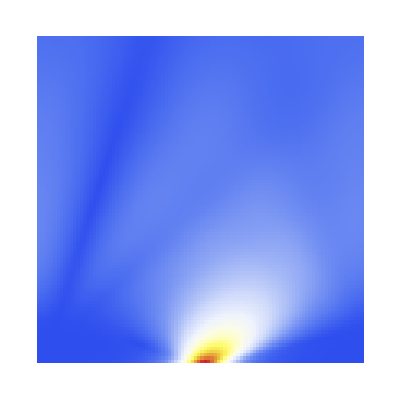

Import::nffil: File not found during Import.

$Failed

ArrayPlot::mat: Argument $Failed at position 1 is not a list of lists.

ArrayPlot[$Failed]

```mathematica
folder = "subfolder3";
name = "a.csv";



location = NotebookDirectory[]<>folder <> "/"<>name
data = Import[location];
ArrayPlot[Reverse[data],ColorFunction-> "TemperatureMap"]
```

```mathematica
Im
```